基礎庫 :

```mathematica
<<(FileNameJoin[{$UserDocumentsDirectory,"Wolfram Mathematica","ssrlib.wl"}])
```

WorkPath :

D:\Work\SSR\_data

## 英雄升级

```mathematica
Clear[herobkExp,heroLvToExp];
herobkExp = Normal[Base`excleData[modelFile,"hero","base"][All,"bkExp"]];
heroLvToExp[lv_Integer]:= Accumulate[heroExp][[lv]] + Total[herobkExp[[;;lv]]];
heroLvToExp[lvList_List]:= Total[heroLvToExp/@lvList];
```

```mathematica
heroLvToExp[{11,11,11}]
```

1950.

3750.

等级时间圖像,單調遞增性：

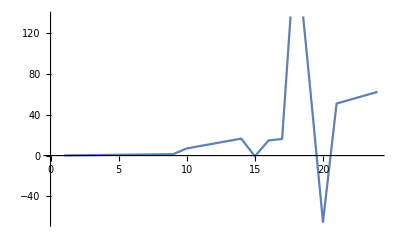
{-Graphics-,False}

```mathematica
{ListLinePlot[Differences@Table[getDayByLv[n],{n,1,maxLv}]],OrderedQ[Differences@Table[getDayByLv[n],{n,1,maxLv}]]}
```

```mathematica
CellPrint[Cell[BoxData[ToBoxes[Piecewise[Table[{funcsLt[[n]],x<=lvconfig[n,"Lv"]},{n,2,Length@funcsLt}]]]],"Abstract"]]
```

Piecewise[{{0.125 x, x≤4.}, {0.246154 x, x≤7.}, {0.270073 x, x≤15.}, {0.437158 x, x≤18.}, {0.745856 x, x≤20.}, {1.08293 x, x≤25.}, {0, True}}]

```mathematica
Differences@Table[funcsMainLv[[Base`excleIndex[lvconfig,"Lv"->n]]]/.x-> n,{n,1,maxLv}]
```

{1.65685,1.27135,1.0718,0.506396,0.778083,0.715521,0.665991,0.625512,0.591624,-1.27096,0.134571,0.129071,0.124195,0.119833,0.177871,0.141862,0.137747,0.864863,0.0564828,-1.05168,0.0781275,0.0763712,0.0747282,0.0731869}

```mathematica
ToExpression/@Import["D:\\Work\\SSR\\_data\\funcsMainLv.txt","Data"]
```

{0,0.+4. x^3,3.98246+0.0175439 x^3,9.85714+0.000416493 x^3,10.7737+0.0000824538 x^3,12.9231+2.849×10^-6 x^3,14.449+7.55858×10^-7 x^3,15.8532+3.39789×10^-7 x^3,17.2228+1.91902×10^-7 x^3,18.5781+1.23047×10^-7 x^3,21.6977+3.62398×10^-8 x^3}

```mathematica
lvconfig
```

## 建造时间

生命周期= 建造时间/(1-config.rely) *(1-config.once) - config.Put_day

```mathematica
ClearAll[speedDay,speedPutByLv,mbtData,mainBuildTime,ssData,rokData];
speedDay[day_/;day==0]:=0;
speedDay[day_]:= Module[{index=Base`excleIndex[lvconfig,"Day"->day]},speedconfig[index-1,"Put_day"]+(day-lvconfig[index-1,"Day"])*speedconfig[index,"_day"]];
speedPutByLv[lv_]:= speedDay[getDayByLv[lv]];
mbtData[lv_]:= Module[{index = Base`excleIndex[lvconfig,"Lv"->lv]},(getDayByLv[lv]+speedPutByLv[lv])/(1-speedconfig[index,"_once"])*(1-speedconfig[index,"rely"]/speedconfig[index,"queue"])];
mainfuc =Fit[Table[{n,mbtData[n]-mbtData[n-1]},{n,1,35}],{1,x,x^2,x^3},x];
ssData = Normal@Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"mainLv","ss_data"][#/24/3600&,"ss"];
mainBuildTime = Join[ssData[[;;12]],Table[mainfuc/.x->n,{n,13,35}]];
rokData = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"mainLv","ss_data"][#/24/3600&,"rok"]//Normal;
rokOri = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"mainLv","ss_data"][#/24/3600&,"rok_ori"]//Normal;
ListLinePlot[{mainBuildTime,ssData,rokData,rokOri},PlotLabels->{"ss_china","ss","rok","rok_ori"},PlotLabel->"建造时间曲线"]
```

$Aborted

```mathematica
ClearAll[speedLvInfo,speedTotal];
speedLvInfo[lv_]:= Module[{during=getDayByLv[lv-1,lv],speedPut=Differences@Table[speedPutByLv[n],{n,0,35}],
relyTime=mainBuildTime[[lv]]*speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"rely"]/(1-speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"rely"]),sciTime=mainBuildTime[[lv]]/(1-speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"rely"])*speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"_once"]},
<|"Lv"->lv,"plan"->during,"mainTime"->mainBuildTime[[lv]],"relyTime"->relyTime,"queueTime"->relyTime*(1-1/speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"queue"]),"speed"->speedPut[[lv]],"sciTime"->sciTime,
"fixSpeed"->mainBuildTime[[lv]]+relyTime/speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"queue"]-speedPut[[lv]]-sciTime-getDayByLv[lv-1,lv],"paySpeed"->during*speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"pay"]/speedconfig[Base`excleIndex[lvconfig,"Lv"->lv],"discount"]|>];
Export[FileNameJoin[{dataPath,"speedLvInfo.txt"}],Table[speedLvInfo[n],{n,1,35}]//Dataset,"Table"]
```

$Aborted

```mathematica
speedTotal = SemanticImport[FileNameJoin[{dataPath,"speedLvInfo.txt"}]][Total,All];
speedPut = speedTotal[{"plan","queueTime","speed","sciTime"}];
labelPut={"生命周期","队列加成","加速投放","科技加成"}+(speedPut//Values//Normal);
speedNeed = speedTotal[{"mainTime","relyTime"}];
labelNeed = {"主堡建造","依赖建造"}+(speedNeed//Values//Normal);
PieChart[Normal/@{speedPut,speedNeed},ChartLabels->Join[PercentForm/@((speedPut//Values//Normal)/Total[speedPut]),labelNeed],ChartLegends->labelPut]
```

-Graphics-

## 付费

付费相关参数 : main.xlsx -> payLv
购买加速：

```mathematica
ClearAll[payconfig,speedLvData,fixSpeed,queueSpeed,paySpeed,speedDayInfo];
payconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"payLv","base"];
speedLvData= SemanticImport[FileNameJoin[{dataPath,"speedLvInfo.txt"}]];
paySpeed[day_]:=speedconfig[Base`excleIndex[lvconfig,"Day"->day],#pay&]/speedconfig[First,"value"]/3600/24;
fixSpeed[day_/;day==1]:=Total@speedLvData[Select[#Lv≤getLvByDay[day]&],"fixSpeed"];
fixSpeed[day_/;day>1]:=speedLvData[SelectFirst[#Lv==Min[maxLv,Round[getLvByDay[day],1]]&],#fixSpeed/#plan&];
queueSpeed[day_/;day==1]:=Total@speedLvData[Select[#Lv≤getLvByDay[day]&],"queueTime"];
queueSpeed[day_/;day>1]:=speedLvData[SelectFirst[#Lv==Min[maxLv,Round[getLvByDay[day],1]]&],#queueTime/#plan&];
```

$Aborted

折扣计算：参考rok  main.xlsx -> payLv -> rok

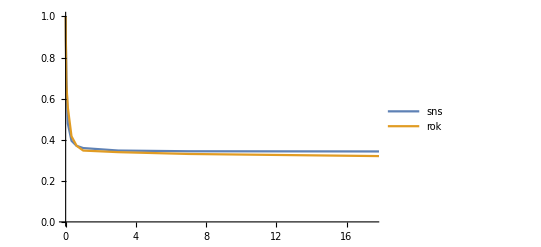

Part::partw: Part 1 of {} does not exist.

Values::invrl: The argument Base`excleIndex[Dataset[«35»],Lv→Min[25.,{}⟦1,1,2⟧]][{{mainTime→0.0019675925925925924,relyTime→(0.0019675925925925924*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},{mainTime→0.003125,relyTime→(0.003125*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},«7»,{mainTime→0.18055555555555555,relyTime→(0.18055555555555555*speedconfig[3, "rely"])/(1 - speedconfig[3, "rely"])},«25»}] is not a valid Association or a list of rules.

Function::slotn: Slot number 2 in Mean[{discount[#1],discount[#2 0.2]}]& cannot be filled from (Mean[{discount[#1],discount[#2 0.2]}]&)[Base`excleIndex[Dataset[«35»],Lv→Min[25.,{}⟦1,1,2⟧]][{{mainTime→0.0019675925925925924,relyTime→(0.0019675925925925924*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},{mainTime→0.003125,relyTime→(0.003125*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},«7»,{mainTime→0.18055555555555555,relyTime→(0.18055555555555555*speedconfig[3, "rely"])/(1 - speedconfig[3, "rely"])},«25»}]].

Part::partw: Part 1 of {} does not exist.

Values::invrl: The argument Base`excleIndex[Dataset[«35»],Lv→Min[25.,{}⟦1,1,2⟧]][{{mainTime→0.0019675925925925924,relyTime→(0.0019675925925925924*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},{mainTime→0.003125,relyTime→(0.003125*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},«7»,{mainTime→0.18055555555555555,relyTime→(0.18055555555555555*speedconfig[3, "rely"])/(1 - speedconfig[3, "rely"])},«25»}] is not a valid Association or a list of rules.

Function::slotn: Slot number 2 in Mean[{discount[#1],discount[#2 0.2]}]& cannot be filled from (Mean[{discount[#1],discount[#2 0.2]}]&)[Base`excleIndex[Dataset[«35»],Lv→Min[25.,{}⟦1,1,2⟧]][{{mainTime→0.0019675925925925924,relyTime→(0.0019675925925925924*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},{mainTime→0.003125,relyTime→(0.003125*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},«7»,{mainTime→0.18055555555555555,relyTime→(0.18055555555555555*speedconfig[3, "rely"])/(1 - speedconfig[3, "rely"])},«25»}]].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Values::invrl: The argument Base`excleIndex[Dataset[«35»],Lv→Min[25.,{}⟦1,1,2⟧]][{{mainTime→0.0019675925925925924,relyTime→(0.0019675925925925924*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},{mainTime→0.003125,relyTime→(0.003125*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},«7»,{mainTime→0.18055555555555555,relyTime→(0.18055555555555555*speedconfig[3, "rely"])/(1 - speedconfig[3, "rely"])},«25»}] is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Function::slotn: Slot number 2 in Mean[{discount[#1],discount[#2 0.2]}]& cannot be filled from (Mean[{discount[#1],discount[#2 0.2]}]&)[Base`excleIndex[Dataset[«35»],Lv→Min[25.,{}⟦1,1,2⟧]][{{mainTime→0.0019675925925925924,relyTime→(0.0019675925925925924*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},{mainTime→0.003125,relyTime→(0.003125*speedconfig[2, "rely"])/(1 - speedconfig[2, "rely"])},«7»,{mainTime→0.18055555555555555,relyTime→(0.18055555555555555*speedconfig[3, "rely"])/(1 - speedconfig[3, "rely"])},«25»}]].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

$Aborted

```mathematica
ClearAll[x,dtconfig,fucDiscount,discount,discountMax];
dtconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"payLv","discount"];
fucDiscount = Fit[dtconfig[All,{"time","ssr"}]//Values//Normal,{1,1/x,1/x^2,1/x^3},x];
discount[time_]:=Module[{result=fucDiscount/.x->time},If[0≤ result≤ 1,result,1]];
discount[time_/;time≤ 0]:=1;
ListLinePlot[{Table[{n,discount[n]},{n,dtconfig[All,"time"]//Normal}],dtconfig[All,{"time","rok"}]//Values//Normal},PlotLegends->{"sns","rok"}]
discountMax[day_/;day>0]:= Mean[{discount@#1,discount[#2*0.2]}]&@@(Base`excleLookUp[speedLvData,"Lv"-> Min[maxLv,getLvByDay[day]],{"mainTime","relyTime"}]//Normal//Values);
discountMax[day_/;day<=0]:=0;
speedDayInfo[day_]:= Module[{speed=speedconfig[Base`excleIndex[lvconfig,"Day"->day],"_day"]+fixSpeed[day],sciTime=speedconfig[Base`excleIndex[lvconfig,"Day"->day],"_once"],paySpeed=paySpeed[day],queue=queueSpeed[day]},<|"day"->day,"queue"->queue,"speed"->speed,"sciTime"->sciTime,"paySpeed"->paySpeed,"maxDiscount"->discountMax[day]|>];
Export[FileNameJoin[{dataPath,"speedDayInfo.txt"}],Table[speedDayInfo[n],{n,1,maxDay+100}]//Dataset,"Table"]
```

付费分层：

```mathematica
ClearAll[expNeedData,expGetData,dayPay,lvDayPay,payData,payLvByDay];
expNeedData = SemanticImport[FileNameJoin[{dataPath,"speedLvInfo.txt"}]][All,#mainTime+#relyTime&]//Normal;
expGetData = SemanticImport[FileNameJoin[{dataPath,"speedDayInfo.txt"}]];
dayPay[day_,pay_]:= expGetData[Select[#day≤day&],(#queue+#speed+1)/(1-#sciTime)+pay*#paySpeed/Min[discount@pay,#maxDiscount]&]//Total;
lvDayPay[day_,pay_]:= Module[{exp=dayPay[day,pay],nextLv},nextLv =First@FirstPosition[Accumulate@expNeedData,n_/;n>=exp,{Length@expNeedData}];
Min[lvconfig[Last,"Lv"],nextLv-1+(exp-Accumulate[expNeedData][[nextLv-1]])/expNeedData[[nextLv]]]];
```

```mathematica
ListLinePlot[ReplacePart[#,FirstPosition[#,n_/;n≥maxLv,IntegerPart@maxDay]->Callout[maxLv,StringForm["``天",First@FirstPosition[#,n_/;n>=maxLv,{maxDay}]],Above]]&/@Transpose@Table[lvDayPay[n,#]&/@Normal[payconfig[All,"payLv"]],{n,1,maxDay}],PlotLegends->payconfig[All,StringForm["``R:``元/日",#name,ToString@#payLv]&]//Normal]
```

-Graphics-

```mathematica
payData = Accumulate@Table[speedconfig[Base`excleIndex[lvconfig,"Day"->n],"pay"],{n,1,maxDay}];
payLvByDay = Prepend[Table[Prepend[{payData[[n]]*#,lvDayPay[n,#]}&/@Normal[payconfig[All,"payLv"]],n],{n,1,maxDay}],Prepend[Normal@payconfig[All,"payLv"],"Day"]];
Export[FileNameJoin[{dataPath,"payLvByDay.txt"}],payLvByDay,"Table"]
(*payInfo = Module[{price=speedconfig[First,"value"]},<|"单价(元/秒)"->price|>];*)
```

$Aborted